```mathematica
<<NumericalCalculus`
```

```mathematica
Λ[x_]=0.3127477*x-0.0231669*x^2-0.0005110 x^3-0.0000045 x^4;
```

10

3

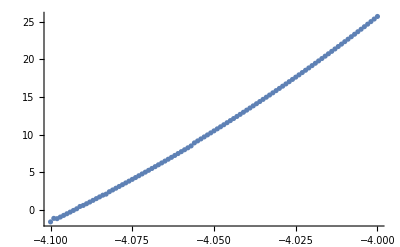

```mathematica
(*Shooting method to find the value for c for a particular value of 'Distance':We desire the solution to match the boundary condition that the derivative needs to be (c-Λ[c])/2, so we find the particular value of c where the solution to the differential equation will satisfy this condition.*)
(*Unfortuantely, the code is manual: it seems like there isn't a good way to determine the "minC" and "maxC" parameters and get good numerical results without inducing an extremely tiny step size that makes the program ridiculously slow.*)
R=10
Distance=3;
minC=-4.1;
maxC=-4;
list={};
list2={};
step=0.001;
Print[Distance];
For[c=minC,c≤maxC,c+=step,
sol=NDSolve[{(ξ^2-1)D[g[ξ],{ξ,2}]+2ξ D[g[ξ],ξ]+(2*Distance* ξ +c ξ^2-Λ[c])g[ξ]==0,g[1.000001]==1,g[R]==0},g,{ξ,1.000001,R}];
temp[ξ_]=g[ξ]/.sol;
AppendTo[list, ND[temp[ξ],ξ,1.000001]-(c-Λ[c])/2];
AppendTo[list2, c];
];
xy=Thread @ {list2,Flatten[list]};
int=Interpolation[xy];
theC=x/.FindRoot[D[int[x]]==0,{x,minC}];
ListPlot[xy]
```

```mathematica
theC
```

-4.09264

```mathematica
4*theC/Distance^2
```

-1.81895

9

InterpolatingFunction[…][ξ]

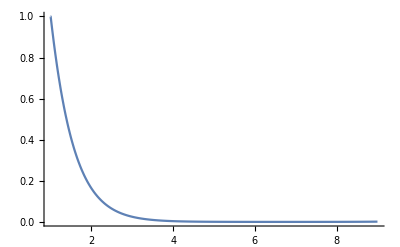

```mathematica
c=theC;
R=9
sol=First[NDSolve[{(ξ^2-1)D[g[ξ],{ξ,2}]+2ξ D[g[ξ],ξ]+(2*Distance* ξ +c ξ^2-Λ[c])g[ξ]==0,g[1.000001]==1,g[R]==0},g,{ξ,1.000001,R}]];
r[ξ_]=g[ξ]/.sol
Plot[r[ξ]/.sol,{ξ,1.000001, R},PlotRange->All]
```

```mathematica
(*angular equation*)
c=theC;
phiSol=First[NDSolve[{(1-η^2)D[f[η],{η,2}]-2η D[f[η],η]-(-Λ[c]+c η^2)f[η]==0,f[0.999999999]==1,f[-0.999999999]==1},f,{η,-0.999999999,0.999999999}]]
```

{f→InterpolatingFunction[…]}

InterpolatingFunction[…][η]

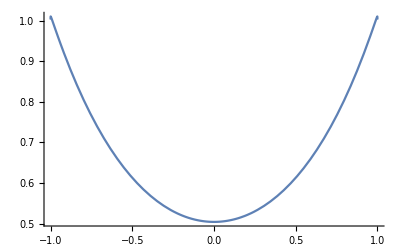

```mathematica
angSol[η_]=f[η]/.phiSol
Plot[angSol[η],{η,-1,1},PlotRange->All]
```

```mathematica
NIntegrate[angSol[η]^2,{η,-0.999999999,0.999999999}]
```

0.916687

```mathematica
NIntegrate[angSol[η]^2 r[ξ]^2 Distance^3/8(ξ^2-η^2),{ξ,1.000001,R},{η,-0.999999999,0.999999999}]
```

1.88586

```mathematica
ra[x_,z_]=√((z+Distance/2)^2+x^2);
rb[x_,z_]=√((z-Distance/2)^2+x^2);
ξ[x_,z_]=(ra[x,z]+rb[x,z])/Distance;
η[x_,z_]=(ra[x,z]-rb[x,z])/Distance;
ψ[ξ_,η_]=r[ξ]*angSol[η]
```

InterpolatingFunction[…][η] InterpolatingFunction[…][ξ]

```mathematica
Plot3D[ψ[ξ,η],{ξ,1.00001, R},{η,-0.999,0.999},PlotRange->All]
```

-Graphics3D-

```mathematica
ξ[0,0]
η[0,0]
```

1

0

```mathematica
ψ[1,0]
```

0.794609

```mathematica
Ψ1[x_,z_]=Piecewise[{{ψ[ξ[x,z],η[x,z]],x>0 && z>0},{ψ[ξ[-x,z],η[-x,z]],x<=0 && z>0},{ψ[ξ[x,-z],η[x,-z]],x>0&&z≤0},{ ψ[ξ[-x,-z],η[-x,-z]],x≤0&&z≤0}}];
```

```mathematica
Plot3D[Ψ1[x,z]^2,{x,-3,3},{z,-3,3},PlotRange->All]
```

-Graphics3D-

```mathematica
M=20;
theN=20;
minX=-3
maxX=3
minY=-3
maxY=3
electronDensity=Table[Ψ1[x,z]^2,{x,minX,maxX,(maxX-minX)/theN},{z,-5,5,(maxY-minY)/M}]*(1/NIntegrate[Ψ1[x,y]^2,{x,minX, maxX},{y,minY, maxY}])
Export[NotebookDirectory[]<>"electronDensity.csv",electronDensity]
```

-3

3

-3

3

/Users/Jessica/git/FiniteElementCode/electronDensity.csv

```mathematica
ListPlot3D[electronDensity,PlotRange->All]
```

-Graphics3D-

# Exporting electron density

```mathematica
M=200;
theN=200;
minX=-5;
maxX=5;
minY=-5;
maxY=5;
electronDensity=N[Table[1/(√(2 π))^3 ⅇ^((-(x^2+y^2))/2),{x,minX,maxX,(maxX-minX)/theN},{y,minY,maxY,(maxY-minY)/M}]]
Export[NotebookDirectory[]<>"electronDensity.csv",electronDensity]
```

{1}
 |  |  |  |

/Users/Jessica/git/FiniteElementCode/electronDensity.csv

```mathematica
ListPlot3D[electronDensity,PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[1/(√(2 π))^3 ⅇ^((-(x^2+y^2))/2),{x,-3,3},{y,-3,3},PlotRange->All]
```

-Graphics3D-

```mathematica
testlist={1,2,3}
```

{1,2,3}

```mathematica
testlist*3
```

{3,6,9}

```mathematica
Clear[f]
sol=NDSolve[{-(D[f[x, y,z],{x,2}]+D[f[x, y,z],{y,2}]+D[f[x, y,z],{z,2}])==1/(√(2 π))^3 ⅇ^((-(x^2+y^2+z^2))/2),DirichletCondition[f[x,y,z]==1/(4 π)1/(√(x^2+y^2+z^2)),True]},f,{x,-5,5},{y,-5,5},{z,-5,5}]
```

{{f→InterpolatingFunction[{{-5., 5.}, {-5., 5.}, {-5., 5.}}, <>]}}

```mathematica
thesol[x_,y_,z_]=f[x, y,z]/.sol
Plot3D[thesol[x,y,0],{x,-5,5},{y,-5,5}]
```

{InterpolatingFunction[{{-5., 5.}, {-5., 5.}, {-5., 5.}}, <>][x,y,z]}

-Graphics3D-

```mathematica
Clear[f]
sol=NDSolve[{-(D[f[x, y],{x,2}]+D[f[x, y],{y,2}])==1/(√(2 π))^3 ⅇ^((-(x^2+y^2))/2),DirichletCondition[f[x,y]==1/(4 π)1/(√(x^2+y^2)),True]},f,{x,-5,5},{y,-5,5}]
```

{{f→InterpolatingFunction[…]}}

```mathematica
Plot3D[f[x,y]/.sol,{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
error[x_,y_]=Abs[1/(4π)1/(√(x^2+y^2))Erf[(√(x^2+y^2))/(√2)]-f[x,y]/.sol]
```

{Abs[Erf[(√(x^2+y^2))/(√2)]/(4 π √(x^2+y^2))-InterpolatingFunction[…][x,y]]}

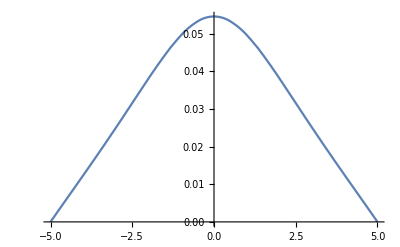

```mathematica
Plot[error[0,y],{y,-5,5}]
```

```mathematica
Plot3D[Abs[1/(4π)1/(√(x^2+y^2))Erf[(√(x^2+y^2))/(√2)]-f[x,y]/.sol],{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
Plot3D[1/(√(2 π))^3 ⅇ^((-(x^2+y^2))/2),{x,-5,5},{y,-5,5},PlotRange->All]
```

-Graphics3D-

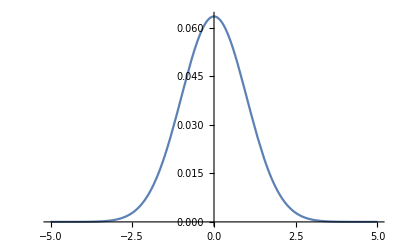

```mathematica
Plot[1/(√(2 π))^3 ⅇ^((-(r^2))/2),{r,-5,5}]
```

```mathematica
test[x_,y_]=f[x,y]/.sol
```

{InterpolatingFunction[…][x,y]}

```mathematica
test[0,0]
```

{0.118112}

```mathematica
sol=NDSolve[{-(D[r^2 D[f[r],r],r])==r^2 1/(√(2 π))^3 ⅇ^((-(r^2))/2),DirichletCondition[f[r]==1/(4 π)1/Abs[r],True]},f,{r,-5,5}]
```

{{f→InterpolatingFunction[…]}}

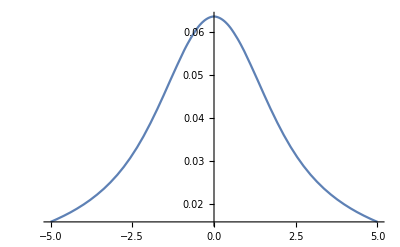

```mathematica
Plot[f[r]/.sol,{r,-5,5}]
```

```mathematica
Plot[1/(√(2 π))^3 ⅇ^((-(r^2))/2),{r,-5,5}]
```

-Graphics-

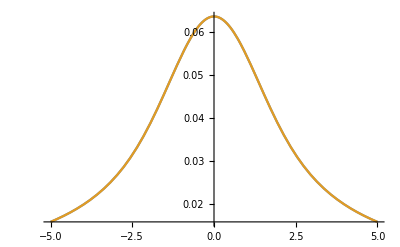

```mathematica
Plot[{1/(4π)1/r Erf[r/(√2)],1/(4π)1/(√(0^2+r^2))Erf[(√(0^2+r^2))/(√2)]},{r,-5,5}]
```

```mathematica
Plot3D[1/(4π)1/(√(x^2+y^2))Erf[(√(x^2+y^2))/(√2)],{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
g[x_,y_]=1/(4π)1/(√(x^2+y^2))Erf[(x^2+y^2)/(√2)]
```

Erf[(x^2+y^2)/(√2)]/(4 π √(x^2+y^2))

```mathematica
g[-0.00001,0.00001]
```

8.97936×10^-7

```mathematica
f[x_,y_,z_]=1/(4π)1/(√(x^2+y^2+z^2))Erf[(√(x^2+y^2+z^2))/(√2)]
```

Erf[(√(x^2+y^2+z^2))/(√2)]/(4 π √(x^2+y^2+z^2))

```mathematica
FullSimplify[-(D[f[x, y,z],{x,2}]+D[f[x, y,z],{y,2}]+D[f[x, y,z],{z,2}])]
```

(ⅇ^(1/2 (-x^2-y^2-z^2)))/(2 √2 π^(3/2))

```mathematica
FullSimplify[FullSimplify[D[f[x, y],{x,2}]]+FullSimplify[D[f[x, y],{y,2}]]]
```

(-(√2 ⅇ^(-x^2/2-y^2/2) (1+x^2+y^2))/(x^2+y^2)+(√π Erf[(√(x^2+y^2))/(√2)])/((x^2+y^2)^(3/2)))/(4 π^(3/2))

```mathematica
FullSimplify[D[f[x, y],{y,2}]]
```

(ⅇ^(1/2 (-x^2-y^2)) (-√(2/π) √(x^2+y^2) (-x^2+(2+x^2) y^2+y^4)-ⅇ^(1/2 (x^2+y^2)) (x^2-2 y^2) Erf[(√(x^2+y^2))/(√2)]))/(4 π (x^2+y^2)^(5/2))

```mathematica
f[r_]=1/(4π)1/r Erf[r/(√2)];
FullSimplify[-1/r^2(D[r^2 D[f[r],r],r])]
```

(ⅇ^(-r^2/2))/(2 √2 π^(3/2))

```mathematica
f[x_,y_]=1/(4π)1/(√(x^2+y^2))Erf[(√(x^2+y^2))/(√2)]
```

Erf[(√(x^2+y^2))/(√2)]/(4 π √(x^2+y^2))

```mathematica
FullSimplify[D[f[x,y],{x,2}]+D[f[x,y],{y,2}]]
```

(-(√2 ⅇ^(-x^2/2-y^2/2) (1+x^2+y^2))/(x^2+y^2)+(√π Erf[(√(x^2+y^2))/(√2)])/((x^2+y^2)^(3/2)))/(4 π^(3/2))

```mathematica
D[x^2,{x,2}]
```

2

```mathematica
FullSimplify[-1/r^2(D[r^2 D[r,r],r])]
```

-2/r

```mathematica
FullSimplify[D[√(x^2+y^2),{x,2}]+D[√(x^2+y^2),{y,2}]]
```

1/(√(x^2+y^2))

```mathematica
y
```

y

```mathematica
FullSimplify[-1/r(D[r D[r,r],r])]
```

-1/r

```mathematica
FullSimplify[D[√(x^2+y^2),{x,2}]+D[√(x^2+y^2),{y,2}]]
```

1/(√(x^2+y^2))